```mathematica
sig=Array[s,{3,3}];
```

```mathematica
KP=KroneckerProduct;
```

```mathematica
KP[IdentityMatrix[2],sig]
```

{{s[1,1],s[1,2],s[1,3],0,0,0},{s[2,1],s[2,2],s[2,3],0,0,0},{s[3,1],s[3,2],s[3,3],0,0,0},{0,0,0,s[1,1],s[1,2],s[1,3]},{0,0,0,s[2,1],s[2,2],s[2,3]},{0,0,0,s[3,1],s[3,2],s[3,3]}}

```mathematica
rho=RandomReal[{0,1},{6,6}]
```

{{0.539199,0.300768,0.47055,0.0155523,0.802345,0.762726},{0.604191,0.739766,0.312804,0.201551,0.0730862,0.742098},{0.904671,0.685634,0.327902,0.824569,0.0746709,0.673955},{0.977401,0.241527,0.466784,0.980466,0.303572,0.690489},{0.352941,0.499546,0.409818,0.0921297,0.141281,0.77398},{0.84027,0.528567,0.188755,0.364929,0.243696,0.265812}}

```mathematica
mat=KP[IdentityMatrix[2],sig]-rho;
```

```mathematica
mat//MatrixForm
```

(-0.539199+s[1,1] | -0.300768+s[1,2] | -0.47055+s[1,3] | -0.0155523 | -0.802345 | -0.762726
-0.604191+s[2,1] | -0.739766+s[2,2] | -0.312804+s[2,3] | -0.201551 | -0.0730862 | -0.742098
-0.904671+s[3,1] | -0.685634+s[3,2] | -0.327902+s[3,3] | -0.824569 | -0.0746709 | -0.673955
-0.977401 | -0.241527 | -0.466784 | -0.980466+s[1,1] | -0.303572+s[1,2] | -0.690489+s[1,3]
-0.352941 | -0.499546 | -0.409818 | -0.0921297+s[2,1] | -0.141281+s[2,2] | -0.77398+s[2,3]
-0.84027 | -0.528567 | -0.188755 | -0.364929+s[3,1] | -0.243696+s[3,2] | -0.265812+s[3,3])

```mathematica
KP[IdentityMatrix[2],sig]
```

{{s[1,1],s[1,2],s[1,3],0,0,0},{s[2,1],s[2,2],s[2,3],0,0,0},{s[3,1],s[3,2],s[3,3],0,0,0},{0,0,0,s[1,1],s[1,2],s[1,3]},{0,0,0,s[2,1],s[2,2],s[2,3]},{0,0,0,s[3,1],s[3,2],s[3,3]}}

```mathematica
d={2,3,4};
```

```mathematica
Times@@dims
```

24

```mathematica
Table[k d[[2]] d[[3]]+l d[[3]]+m,{k,0,d[[1]]-1},{l,0,d[[2]]-1},{m,0,d[[3]]-1}]//Flatten
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23}

```mathematica
tr0=SparseArray[#->1&/@(#+{1,1}&/@Transpose[{Flatten[Table[(Times@@dims)(t d[[1]] d[[2]]+d[[1]]s+n)+(m d[[1]] d[[2]]+d[[1]]l+k),{k,0,d[[1]]-1},{l,0,d[[2]]-1},{m,0,d[[3]]-1},{n,0,d[[1]]-1},{s,0,d[[2]]-1},{t,0,d[[3]]-1}]],Flatten[Table[(Times@@dims)(t d[[1]] d[[2]]+d[[1]]s+n)+(m d[[1]] d[[2]]+d[[1]]l+k),{k,0,d[[1]]-1},{l,0,d[[2]]-1},{m,0,d[[3]]-1},{n,0,d[[1]]-1},{s,0,d[[2]]-1},{t,0,d[[3]]-1}]]}])];
```

```mathematica
tr=SparseArray[#->1&/@(#+{1,1}&/@Transpose[{Flatten[Table[(Times@@dims)(t d[[1]] d[[2]]+d[[1]]s+n)+(m d[[1]] d[[2]]+d[[1]]l+k),{k,0,d[[1]]-1},{l,0,d[[2]]-1},{m,0,d[[3]]-1},{n,0,d[[1]]-1},{s,0,d[[2]]-1},{t,0,d[[3]]-1}]],Flatten[Table[(Times@@dims)(t d[[1]] d[[2]]+d[[1]]l+n)+(m d[[1]] d[[2]]+d[[1]]s+k),{k,0,d[[1]]-1},{l,0,d[[2]]-1},{m,0,d[[3]]-1},{n,0,d[[1]]-1},{s,0,d[[2]]-1},{t,0,d[[3]]-1}]]}])]
```

SparseArray[…]

```mathematica
tr0==IdentityMatrix[576]
```

True

```mathematica
#[[1]]&/@ArrayRules[tr]//Transpose
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511,512,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,556,557,558,559,560,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,576,_},{1,2,49,50,97,98,7,8,55,56,103,104,13,14,61,62,109,110,19,20,67,68,115,116,25,26,73,74,121,122,31,32,79,80,127,128,37,38,85,86,133,134,43,44,91,92,139,140,3,4,51,52,99,100,9,10,57,58,105,106,15,16,63,64,111,112,21,22,69,70,117,118,27,28,75,76,123,124,33,34,81,82,129,130,39,40,87,88,135,136,45,46,93,94,141,142,5,6,53,54,101,102,11,12,59,60,107,108,17,18,65,66,113,114,23,24,71,72,119,120,29,30,77,78,125,126,35,36,83,84,131,132,41,42,89,90,137,138,47,48,95,96,143,144,145,146,193,194,241,242,151,152,199,200,247,248,157,158,205,206,253,254,163,164,211,212,259,260,169,170,217,218,265,266,175,176,223,224,271,272,181,182,229,230,277,278,187,188,235,236,283,284,147,148,195,196,243,244,153,154,201,202,249,250,159,160,207,208,255,256,165,166,213,214,261,262,171,172,219,220,267,268,177,178,225,226,273,274,183,184,231,232,279,280,189,190,237,238,285,286,149,150,197,198,245,246,155,156,203,204,251,252,161,162,209,210,257,258,167,168,215,216,263,264,173,174,221,222,269,270,179,180,227,228,275,276,185,186,233,234,281,282,191,192,239,240,287,288,289,290,337,338,385,386,295,296,343,344,391,392,301,302,349,350,397,398,307,308,355,356,403,404,313,314,361,362,409,410,319,320,367,368,415,416,325,326,373,374,421,422,331,332,379,380,427,428,291,292,339,340,387,388,297,298,345,346,393,394,303,304,351,352,399,400,309,310,357,358,405,406,315,316,363,364,411,412,321,322,369,370,417,418,327,328,375,376,423,424,333,334,381,382,429,430,293,294,341,342,389,390,299,300,347,348,395,396,305,306,353,354,401,402,311,312,359,360,407,408,317,318,365,366,413,414,323,324,371,372,419,420,329,330,377,378,425,426,335,336,383,384,431,432,433,434,481,482,529,530,439,440,487,488,535,536,445,446,493,494,541,542,451,452,499,500,547,548,457,458,505,506,553,554,463,464,511,512,559,560,469,470,517,518,565,566,475,476,523,524,571,572,435,436,483,484,531,532,441,442,489,490,537,538,447,448,495,496,543,544,453,454,501,502,549,550,459,460,507,508,555,556,465,466,513,514,561,562,471,472,519,520,567,568,477,478,525,526,573,574,437,438,485,486,533,534,443,444,491,492,539,540,449,450,497,498,545,546,455,456,503,504,551,552,461,462,509,510,557,558,467,468,515,516,563,564,473,474,521,522,569,570,479,480,527,528,575,576,_}}

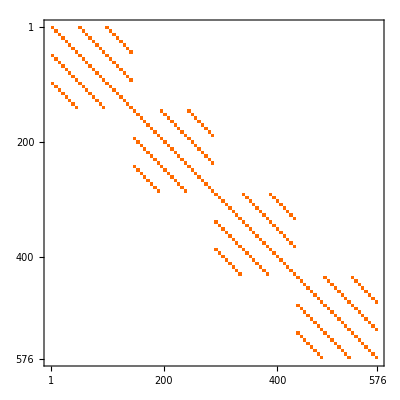

```mathematica
MatrixPlot[tr]
```

```mathematica
SparseArray[{Flatten[Table[(Times@@dims)(t d[[1]] d[[2]]+d[[1]]s+n)+(m d[[1]] d[[2]]+d[[1]]l+k),{k,0,d[[1]]-1},{l,0,d[[2]]-1},{m,0,d[[3]]-1},{n,0,d[[1]]-1},{s,0,d[[2]]-1},{t,0,d[[3]]-1}]],Flatten[Table[(Times@@dims)(t d[[1]] d[[2]]+d[[1]]l+n)+(m d[[1]] d[[2]]+d[[1]]s+k),{k,0,d[[1]]-1},{l,0,d[[2]]-1},{m,0,d[[3]]-1},{n,0,d[[1]]-1},{s,0,d[[2]]-1},{t,0,d[[3]]-1}]]}//Transpose,
```

{{0,0},{144,144},{288,288},{432,432},{48,2},{192,146},{336,290},{480,434},{96,4},{240,148},{384,292},{528,436},{24,24},{168,168},{312,312},{456,456},{72,26},{216,170},{360,314},{504,458},{120,28},{264,172},{408,316},{552,460},{6,6},{150,150},{294,294},{438,438},{54,8},{198,152},{342,296},{486,440},{102,10},{246,154},{390,298},{534,442},{30,30},{174,174},{318,318},{462,462},{78,32},{222,176},{366,320},{510,464},{126,34},{270,178},{414,322},{558,466},{12,12},{156,156},{300,300},{444,444},{60,14},{204,158},{348,302},{492,446},{108,16},{252,160},{396,304},{540,448},{36,36},{180,180},{324,324},{468,468},{84,38},{228,182},{372,326},{516,470},{132,40},{276,184},{420,328},{564,472},{18,18},{162,162},{306,306},{450,450},{66,20},{210,164},{354,308},{498,452},{114,22},{258,166},{402,310},{546,454},{42,42},{186,186},{330,330},{474,474},{90,44},{234,188},{378,332},{522,476},{138,46},{282,190},{426,334},{570,478},{2,48},{146,192},{290,336},{434,480},{50,50},{194,194},{338,338},{482,482},{98,52},{242,196},{386,340},{530,484},{26,72},{170,216},{314,360},{458,504},{74,74},{218,218},{362,362},{506,506},{122,76},{266,220},{410,364},{554,508},{8,54},{152,198},{296,342},{440,486},{56,56},{200,200},{344,344},{488,488},{104,58},{248,202},{392,346},{536,490},{32,78},{176,222},{320,366},{464,510},{80,80},{224,224},{368,368},{512,512},{128,82},{272,226},{416,370},{560,514},{14,60},{158,204},{302,348},{446,492},{62,62},{206,206},{350,350},{494,494},{110,64},{254,208},{398,352},{542,496},{38,84},{182,228},{326,372},{470,516},{86,86},{230,230},{374,374},{518,518},{134,88},{278,232},{422,376},{566,520},{20,66},{164,210},{308,354},{452,498},{68,68},{212,212},{356,356},{500,500},{116,70},{260,214},{404,358},{548,502},{44,90},{188,234},{332,378},{476,522},{92,92},{236,236},{380,380},{524,524},{140,94},{284,238},{428,382},{572,526},{4,96},{148,240},{292,384},{436,528},{52,98},{196,242},{340,386},{484,530},{100,100},{244,244},{388,388},{532,532},{28,120},{172,264},{316,408},{460,552},{76,122},{220,266},{364,410},{508,554},{124,124},{268,268},{412,412},{556,556},{10,102},{154,246},{298,390},{442,534},{58,104},{202,248},{346,392},{490,536},{106,106},{250,250},{394,394},{538,538},{34,126},{178,270},{322,414},{466,558},{82,128},{226,272},{370,416},{514,560},{130,130},{274,274},{418,418},{562,562},{16,108},{160,252},{304,396},{448,540},{64,110},{208,254},{352,398},{496,542},{112,112},{256,256},{400,400},{544,544},{40,132},{184,276},{328,420},{472,564},{88,134},{232,278},{376,422},{520,566},{136,136},{280,280},{424,424},{568,568},{22,114},{166,258},{310,402},{454,546},{70,116},{214,260},{358,404},{502,548},{118,118},{262,262},{406,406},{550,550},{46,138},{190,282},{334,426},{478,570},{94,140},{238,284},{382,428},{526,572},{142,142},{286,286},{430,430},{574,574},{1,1},{145,145},{289,289},{433,433},{49,3},{193,147},{337,291},{481,435},{97,5},{241,149},{385,293},{529,437},{25,25},{169,169},{313,313},{457,457},{73,27},{217,171},{361,315},{505,459},{121,29},{265,173},{409,317},{553,461},{7,7},{151,151},{295,295},{439,439},{55,9},{199,153},{343,297},{487,441},{103,11},{247,155},{391,299},{535,443},{31,31},{175,175},{319,319},{463,463},{79,33},{223,177},{367,321},{511,465},{127,35},{271,179},{415,323},{559,467},{13,13},{157,157},{301,301},{445,445},{61,15},{205,159},{349,303},{493,447},{109,17},{253,161},{397,305},{541,449},{37,37},{181,181},{325,325},{469,469},{85,39},{229,183},{373,327},{517,471},{133,41},{277,185},{421,329},{565,473},{19,19},{163,163},{307,307},{451,451},{67,21},{211,165},{355,309},{499,453},{115,23},{259,167},{403,311},{547,455},{43,43},{187,187},{331,331},{475,475},{91,45},{235,189},{379,333},{523,477},{139,47},{283,191},{427,335},{571,479},{3,49},{147,193},{291,337},{435,481},{51,51},{195,195},{339,339},{483,483},{99,53},{243,197},{387,341},{531,485},{27,73},{171,217},{315,361},{459,505},{75,75},{219,219},{363,363},{507,507},{123,77},{267,221},{411,365},{555,509},{9,55},{153,199},{297,343},{441,487},{57,57},{201,201},{345,345},{489,489},{105,59},{249,203},{393,347},{537,491},{33,79},{177,223},{321,367},{465,511},{81,81},{225,225},{369,369},{513,513},{129,83},{273,227},{417,371},{561,515},{15,61},{159,205},{303,349},{447,493},{63,63},{207,207},{351,351},{495,495},{111,65},{255,209},{399,353},{543,497},{39,85},{183,229},{327,373},{471,517},{87,87},{231,231},{375,375},{519,519},{135,89},{279,233},{423,377},{567,521},{21,67},{165,211},{309,355},{453,499},{69,69},{213,213},{357,357},{501,501},{117,71},{261,215},{405,359},{549,503},{45,91},{189,235},{333,379},{477,523},{93,93},{237,237},{381,381},{525,525},{141,95},{285,239},{429,383},{573,527},{5,97},{149,241},{293,385},{437,529},{53,99},{197,243},{341,387},{485,531},{101,101},{245,245},{389,389},{533,533},{29,121},{173,265},{317,409},{461,553},{77,123},{221,267},{365,411},{509,555},{125,125},{269,269},{413,413},{557,557},{11,103},{155,247},{299,391},{443,535},{59,105},{203,249},{347,393},{491,537},{107,107},{251,251},{395,395},{539,539},{35,127},{179,271},{323,415},{467,559},{83,129},{227,273},{371,417},{515,561},{131,131},{275,275},{419,419},{563,563},{17,109},{161,253},{305,397},{449,541},{65,111},{209,255},{353,399},{497,543},{113,113},{257,257},{401,401},{545,545},{41,133},{185,277},{329,421},{473,565},{89,135},{233,279},{377,423},{521,567},{137,137},{281,281},{425,425},{569,569},{23,115},{167,259},{311,403},{455,547},{71,117},{215,261},{359,405},{503,549},{119,119},{263,263},{407,407},{551,551},{47,139},{191,283},{335,427},{479,571},{95,141},{239,285},{383,429},{527,573},{143,143},{287,287},{431,431},{575,575}}

```mathematica
Flatten[Table[(Times@@dims)(t d[[1]] d[[2]]+d[[1]]l+n)+(m d[[1]] d[[2]]+d[[1]]s+k),{k,0,d[[1]]-1},{l,0,d[[2]]-1},{m,0,d[[3]]-1},{n,0,d[[1]]-1},{s,0,d[[2]]-1},{t,0,d[[3]]-1}]]
```

{0,144,288,432,2,146,290,434,4,148,292,436,24,168,312,456,26,170,314,458,28,172,316,460,6,150,294,438,8,152,296,440,10,154,298,442,30,174,318,462,32,176,320,464,34,178,322,466,12,156,300,444,14,158,302,446,16,160,304,448,36,180,324,468,38,182,326,470,40,184,328,472,18,162,306,450,20,164,308,452,22,166,310,454,42,186,330,474,44,188,332,476,46,190,334,478,48,192,336,480,50,194,338,482,52,196,340,484,72,216,360,504,74,218,362,506,76,220,364,508,54,198,342,486,56,200,344,488,58,202,346,490,78,222,366,510,80,224,368,512,82,226,370,514,60,204,348,492,62,206,350,494,64,208,352,496,84,228,372,516,86,230,374,518,88,232,376,520,66,210,354,498,68,212,356,500,70,214,358,502,90,234,378,522,92,236,380,524,94,238,382,526,96,240,384,528,98,242,386,530,100,244,388,532,120,264,408,552,122,266,410,554,124,268,412,556,102,246,390,534,104,248,392,536,106,250,394,538,126,270,414,558,128,272,416,560,130,274,418,562,108,252,396,540,110,254,398,542,112,256,400,544,132,276,420,564,134,278,422,566,136,280,424,568,114,258,402,546,116,260,404,548,118,262,406,550,138,282,426,570,140,284,428,572,142,286,430,574,1,145,289,433,3,147,291,435,5,149,293,437,25,169,313,457,27,171,315,459,29,173,317,461,7,151,295,439,9,153,297,441,11,155,299,443,31,175,319,463,33,177,321,465,35,179,323,467,13,157,301,445,15,159,303,447,17,161,305,449,37,181,325,469,39,183,327,471,41,185,329,473,19,163,307,451,21,165,309,453,23,167,311,455,43,187,331,475,45,189,333,477,47,191,335,479,49,193,337,481,51,195,339,483,53,197,341,485,73,217,361,505,75,219,363,507,77,221,365,509,55,199,343,487,57,201,345,489,59,203,347,491,79,223,367,511,81,225,369,513,83,227,371,515,61,205,349,493,63,207,351,495,65,209,353,497,85,229,373,517,87,231,375,519,89,233,377,521,67,211,355,499,69,213,357,501,71,215,359,503,91,235,379,523,93,237,381,525,95,239,383,527,97,241,385,529,99,243,387,531,101,245,389,533,121,265,409,553,123,267,411,555,125,269,413,557,103,247,391,535,105,249,393,537,107,251,395,539,127,271,415,559,129,273,417,561,131,275,419,563,109,253,397,541,111,255,399,543,113,257,401,545,133,277,421,565,135,279,423,567,137,281,425,569,115,259,403,547,117,261,405,549,119,263,407,551,139,283,427,571,141,285,429,573,143,287,431,575}